```mathematica
Electrical circuit problem:
Finding condition for resonance of V(L):
Remove[L,R,w0]
```

```mathematica
D[w^2/(√((w0^2-w^2)^2+(R*w/L)^2)),w]
```

```mathematica
-(w^2 ((2 R^2 w)/L^2-4 w (-w^2+w0^2)))/(2 ((R^2 w^2)/L^2+(-w^2+w0^2)^2)^(3/2))+(2 w)/(√((R^2 w^2)/L^2+(-w^2+w0^2)^2))
```

```mathematica
Simplify[-(w^2 ((2 R^2 w)/L^2-4 w (-w^2+w0^2)))/(2 ((R^2 w^2)/L^2+(-w^2+w0^2)^2)^(3/2))+(2 w)/(√((R^2 w^2)/L^2+(-w^2+w0^2)^2))]
```

```mathematica
(R^2 w^3+2 L^2 w w0^2 (-w^2+w0^2))/(√((R^2 w^2)/L^2+(w^2-w0^2)^2) (R^2 w^2+L^2 (w^2-w0^2)^2))
```

5

1

## Showing when VL has a resonance frequency:

```mathematica
R=√2*L*w0-20
```

11.6228

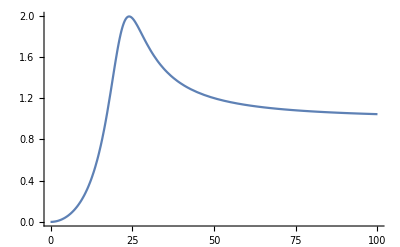

1

1

1

```mathematica
Plot[w^2/(√((w0^2-w^2)^2+(R*w/L)^2)),{w,0,100},PlotRange->All]
```

## showing when VL has no resonance frequency (condition proved in paper):

```mathematica
R=√2*L*w0+20
```

51.6228

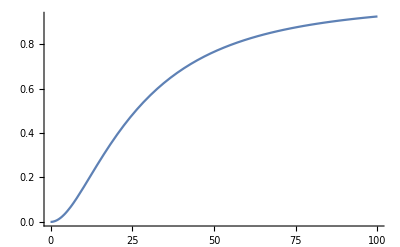

```mathematica
Plot[w^2/(√((w0^2-w^2)^2+(R*w/L)^2)),{w,0,100},PlotRange->All]
```

## Plots for V_L(t), V_R(t), V_c(t): 1. For w_external= w_0

30

0.2

0.0001

100

223.607

223.607

0.0149071

1.5708

0.0149071 Cos[1.5708-223.607 t]

3.33333 Sin[1.5708-223.607 t]

2.35702

100. Sin[1.5708-223.607 t]

70.7107

149.071 Cos[1.5708-223.607 t]

105.409

-149.071 Cos[1.5708-223.607 t]

105.409

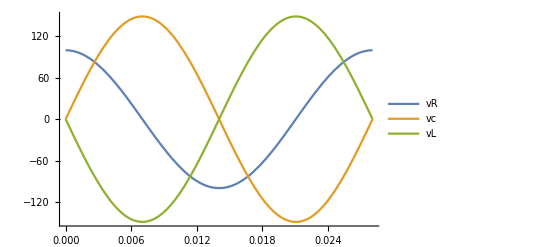

```mathematica
R=30
L=0.2
c=0.0001
V0=100
w0=1/(√(L*c))
w=w0
q0=V0/(L*√((w0^2-w^2)^2+((R*w)/L)^2))
ϕ=ArcSin[R/Sqrt[(w*L-1/(w*c))^2+R^2]]
q=q0*Cos[w*t-ϕ]
i=D[q,t]
irms=(V0*w/(√2))/(L*√((w0^2-w^2)^2+((R*w)/L)^2))
vR=i*R
VR=irms*R
vc=q/c
Vc=irms/(w*c)
vL=L*D[i,t]
VL=(V0*w^2/(√2))/(√((w0^2-w^2)^2+((R*w)/L)^2))
Plot[{vR,vc,vL},{t,0,2*Pi/w},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
2.For Subscript[w, external]~0:
```

0.1

0.01

0.0003

0.01 Cos[0.0003-0.1 t]

0.001 Sin[0.0003-0.1 t]

-0.00002 Cos[0.0003-0.1 t]

100. Cos[0.0003-0.1 t]

0.03 Sin[0.0003-0.1 t]

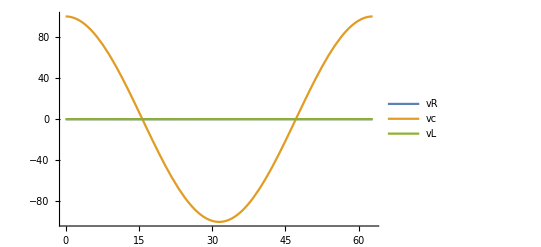

```mathematica
w=0.1
q0=V0/(L*√((w0^2-w^2)^2+((R*w)/L)^2))
ϕ=ArcSin[R/Sqrt[(w*L-1/(w*c))^2+R^2]]
q=q0*Cos[w*t-ϕ]
i=D[q,t]
vL=L*D[i,t]
vc=q/c
vR=i*R
Plot[{vR,vc,vL},{t,0,2*Pi/w},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
3.For Subscript[w, external]-> ∞
```

30000

5.55579×10^-7

0.00500024

5.55579×10^-7 Cos[0.00500024-30000 t]

0.0166674 Sin[0.00500024-30000 t]

-100.004 Cos[0.00500024-30000 t]

0.00555579 Cos[0.00500024-30000 t]

0.500022 Sin[0.00500024-30000 t]

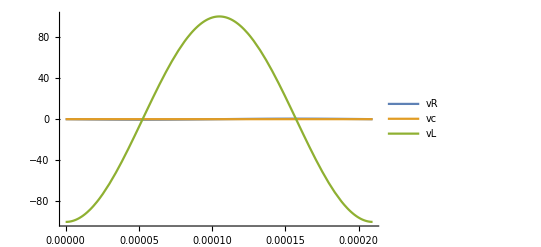

```mathematica
w=30000
q0=V0/(L*√((w0^2-w^2)^2+((R*w)/L)^2))
ϕ=ArcSin[R/Sqrt[(w*L-1/(w*c))^2+R^2]]
q=q0*Cos[w*t-ϕ]
i=D[q,t]
vL=L*D[i,t]
vc=q/c
vR=i*R
Plot[{vR,vc,vL},{t,0,2*Pi/w},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
4. For Subscript[w, external]~ Subscript[w, capacitive resonant]:
```

196.85

0.0158238

1.20678

0.0158238 Cos[1.20678-196.85 t]

3.11491 Sin[1.20678-196.85 t]

-122.634 Cos[1.20678-196.85 t]

158.238 Cos[1.20678-196.85 t]

93.4473 Sin[1.20678-196.85 t]

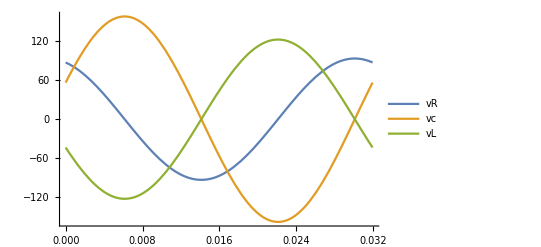

```mathematica
w=√(1/(L*c)-R^2/(2 L^2))
q0=V0/(L*√((w0^2-w^2)^2+((R*w)/L)^2))
ϕ=ArcSin[R/Sqrt[(w*L-1/(w*c))^2+R^2]]
q=q0*Cos[w*t-ϕ]
i=D[q,t]
vL=L*D[i,t]
vc=q/c
vR=i*R
Plot[{vR,vc,vL},{t,0,2*Pi/w},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
5. For Subscript[w, external]~ Subscript[w, inductive resonance]:
```

254.

0.0122634

1.20678

0.0122634 Cos[1.20678-254. t]

3.11491 Sin[1.20678-254. t]

-158.238 Cos[1.20678-254. t]

122.634 Cos[1.20678-254. t]

93.4473 Sin[1.20678-254. t]

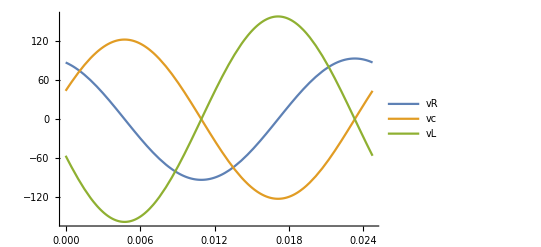

```mathematica
w=√((2 L^2*w0^4)/(2 L^2*w0^2-R^2))
q0=V0/(L*√((w0^2-w^2)^2+((R*w)/L)^2))
ϕ=ArcSin[R/Sqrt[(w*L-1/(w*c))^2+R^2]]
q=q0*Cos[w*t-ϕ]
i=D[q,t]
vL=L*D[i,t]
vc=q/c
vR=i*R
Plot[{vR,vc,vL},{t,0,2*Pi/w},PlotLegends->"Expressions",PlotRange->All]
```